# Finite-length longitudinal PEEC

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

Z=R+jωL; Zi=V1; 1ᵀi=It

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Change length or cross divisions; compare complex port constraints and power. The basis is longitudinal.

## Derivation and interpretation

Discretize the cross section into longitudinal current basis elements. Galerkin projection of the magnetoquasistatic integral equation gives Z=R+jωL, where R follows from conductivity and basis overlap and L contains finite-length mutual and self interactions.

Solve Zi=V1 and 1ᵀi=It simultaneously. The terminal voltage and complex currents are unknowns. Real input power must equal the quadratic resistive loss iᴴRi.

Vary cross-section divisions, longitudinal length and quadrature independently. This longitudinal basis omits general transverse current and end-region charge; it must not be presented as a full vector 3D conductor solution.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"cross_divisions"->6,"length_m"->0.04,"frequency_Hz"->200000.,"quadrature_order"->4|>;parameters
```

<|cross_divisions -> 6, length_m -> 0.04, frequency_Hz -> 200000., 
 
>   quadrature_order -> 4|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"peec",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_peec_20261014075036_ffc0b9bc, 
 
>   source_model -> finite_length_longitudinal_volume_filament_PEEC, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

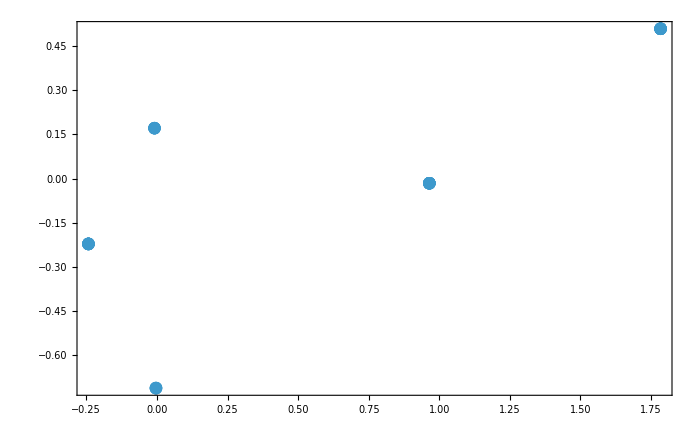

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: P03, RUEHLI1974; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch peec